```mathematica
Clear[PowerPoly];PowerPoly[n_,v_]:=PowerPoly[n,v]=Expand[(x-v)^(n-1)]
```

```mathematica
Table[PowerPoly[n],{n,1,5}]
```

{1,-3+x,9-6 x+x^2,-27+27 x-9 x^2+x^3,81-108 x+54 x^2-12 x^3+x^4}

```mathematica
PowerCoeff[p_,n_:3]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p,count},
For[pos=degree,pos≥1,pos--,
current = PowerPoly[pos+1,n];
count=PolynomialQuotient[poly,current,x];
poly=PolynomialRemainder[poly,current,x];
result=Append[result,count];
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
ChromaticPolynomial[CompleteGraph[4],x]
```

-6 x+11 x^2-6 x^3+x^4

```mathematica
PolynomialQuotient[-6 x+11 x^2-6 x^3+x^4,81-108 x+54 x^2-12 x^3+x^4,x]
```

1

```mathematica
-6 x+11 x^2-6 x^3+x^4-(81-108 x+54 x^2-12 x^3+x^4)
```

-81+102 x-43 x^2+6 x^3

```mathematica
PolynomialQuotient[-81+102 x-43 x^2+6 x^3,-27+27 x-9 x^2+x^3,x]
```

6

```mathematica
allGraphs5[0,"children"]
```

{{19683,39366},{6561,13122},{2187,4374},{729,1458},{243,486},{81,162},{27,54},{9,18},{3,6},{1,2}}

```mathematica
PowerCoeff[ChromaticPolynomial[allGraphs5[0,"graph"],x],5]/5
```

{625,625,250,50,5,1/5}

```mathematica
PowerCoeff[ChromaticPolynomial[allGraphs5[19683,"graph"],x],5]/5
```

{500,525,220,46,24/5,1/5}

```mathematica
ChromaticPolynomial[allGraphs5[19683,"graph"],x]
```

-x^4+x^5

```mathematica
Length[PowerCoeff[ChromaticPolynomial[Graph[plantri[[8]]],x],5]]
```

18

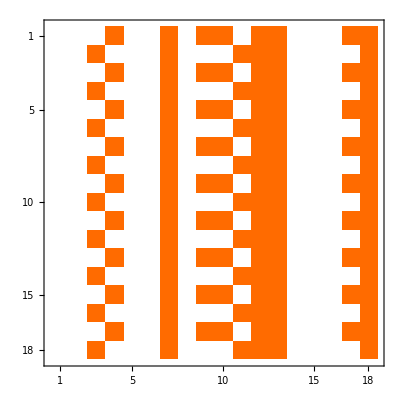

```mathematica
With[
{p=ChromaticPolynomial[Graph[plantri[[8]]],x]},
MatrixPlot[Table[Map[Mod[#,2]&,PowerCoeff[p,k]],{k,0,17}]]
]
```

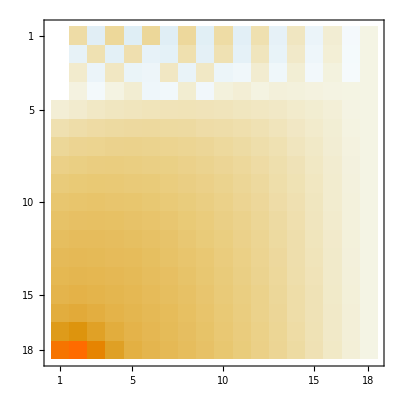

```mathematica
With[
{p=ChromaticPolynomial[Graph[plantri[[8]]],x]},
MatrixPlot[Table[PowerCoeff[p,k],{k,0,17}]]
]
```

```mathematica
With[
{p=ChromaticPolynomial[Graph[plantri[[8]]],x]},
MatrixRank[Table[PowerCoeff[p,k],{k,0,20}]]
]
```

18

```mathematica
TableForm[Table[With[
{chrom=ChromaticPolynomial[allGraphs6[k,"graph"],x]},
PowerCoeff[chrom,3]->Total[PowerCoeff[chrom,3]]->PowerCoeff[chrom,4]
],{k,Select[Keys[allGraphs5],VertexCount[allGraphs6[#,"graph"]]==6&]}]//Tally//Sort,TableDepth->2]
```

{0,-18,-21,10,20,8,1}→0→{0,96,224,190,75,14,1} | 1
{0,0,18,39,29,9,1}→96→{96,320,414,265,89,15,1} | 10
{0,18,57,68,38,10,1}→192→{192,544,604,340,103,16,1} | 30
{0,36,96,97,47,11,1}→288→{288,768,794,415,117,17,1} | 20
{0,54,135,126,56,12,1}→384→{384,992,984,490,131,18,1} | 5
{18,57,86,77,39,10,1}→288→{288,672,666,353,104,16,1} | 15
{18,75,125,106,48,11,1}→384→{384,896,856,428,118,17,1} | 70
{36,114,154,115,49,11,1}→480→{480,1024,918,441,119,17,1} | 30
{36,132,193,144,58,12,1}→576→{576,1248,1108,516,133,18,1} | 135
{54,171,222,153,59,12,1}→672→{672,1376,1170,529,134,18,1} | 60
{54,189,261,182,68,13,1}→768→{768,1600,1360,604,148,19,1} | 30
{72,228,290,191,69,13,1}→864→{864,1728,1422,617,149,19,1} | 150
{90,231,259,163,60,12,1}→816→{816,1544,1243,543,135,18,1} | 10
{90,267,319,200,70,13,1}→960→{960,1856,1484,630,150,19,1} | 12
{108,288,327,201,70,13,1}→1008→{1008,1896,1495,631,150,19,1} | 60
{108,324,387,238,80,14,1}→1152→{1152,2208,1736,718,165,20,1} | 70
{144,384,424,248,81,14,1}→1296→{1296,2376,1809,732,166,20,1} | 125
{162,405,432,249,81,14,1}→1344→{1344,2416,1820,733,166,20,1} | 15
{162,459,513,294,92,15,1}→1536→{1536,2816,2112,832,182,21,1} | 10
{216,540,558,305,93,15,1}→1728→{1728,3024,2196,847,183,21,1} | 110
{324,756,729,372,106,16,1}→2304→{2304,3840,2656,976,201,22,1} | 45
{486,1053,945,450,120,17,1}→3072→{3072,4864,3200,1120,220,23,1} | 10
{729,1458,1215,540,135,18,1}→4096→{4096,6144,3840,1280,240,24,1} | 1

```mathematica
ChromaticPolynomial[MinimalGraph[3],x]
```

-6 x+11 x^2-6 x^3+x^4

```mathematica
FindFullFormula[MinimalGraph[5]]
```

{v1x2x3x4x5x6,v1x2x3x46x5,v1x2x36x4x5,v1x2x35x4x6,v1x2x35x46}

```mathematica
Table[PowerCoeff[ChromaticPolynomial[MinimalGraph[k],x],3],{k,2,10}]//MatrixForm
```

({6,11,6,1}
{0,6,11,6,1}
{0,0,6,11,6,1}
{0,0,0,6,11,6,1}
{0,0,0,0,6,11,6,1}
{0,0,0,0,0,6,11,6,1}
{0,0,0,0,0,0,6,11,6,1}
{0,0,0,0,0,0,0,6,11,6,1}
{0,0,0,0,0,0,0,0,6,11,6,1})

```mathematica
Table[PowerCoeff[ChromaticPolynomial[CompleteGraph[k],x],3],{k,10}]//MatrixForm
```

({3,1}
{6,5,1}
{6,11,6,1}
{0,6,11,6,1}
{0,-6,-5,5,5,1}
{0,12,4,-15,-5,3,1}
{0,-36,0,49,0,-14,0,1}
{0,144,-36,-196,49,56,-14,-4,1}
{0,-720,324,944,-441,-231,126,6,-9,1}
{0,4320,-2664,-5340,3590,945,-987,90,60,-15,1})

```mathematica
Table[PowerCoeff[ChromaticPolynomial[WheelGraph[k],x],3],{k,10}]//MatrixForm
```

({3,1}
{0}
{6,11,6,1}
{0,6,11,6,1}
{6,17,23,18,7,1}
{0,12,34,40,25,8,1}
{6,23,52,75,65,33,9,1}
{0,18,69,126,140,98,42,10,1}
{6,29,93,196,266,238,140,52,11,1}
{0,24,116,288,462,504,378,192,63,12,1})

```mathematica
Table[PadLeft[PowerCoeff[ChromaticPolynomial[JacobsThalGraph[k],x],3],20],{k,2,20,2}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 23 | 28 | 19 | 13 | 6 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 29 | 57 | 76 | 65 | 33 | 15 | 6 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 35 | 98 | 197 | 266 | 238 | 140 | 52 | 17 | 6 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 41 | 151 | 406 | 750 | 966 | 882 | 570 | 255 | 75 | 19 | 6 | 1
0 | 0 | 0 | 0 | 0 | 6 | 47 | 216 | 727 | 1705 | 2871 | 3564 | 3300 | 2277 | 1155 | 418 | 102 | 21 | 6 | 1
0 | 0 | 0 | 6 | 53 | 293 | 1184 | 3367 | 7007 | 11011 | 13299 | 12441 | 9009 | 5005 | 2093 | 637 | 133 | 23 | 6 | 1
0 | 6 | 59 | 382 | 1801 | 6020 | 14924 | 28392 | 42328 | 50050 | 47190 | 35464 | 21112 | 9828 | 3500 | 920 | 168 | 25 | 6 | 1
65 | 483 | 2602 | 9996 | 28764 | 64260 | 114036 | 163098 | 189618 | 179894 | 139230 | 87516 | 44268 | 17748 | 5508 | 1275 | 207 | 27 | 6 | 1
3611 | 15675 | 51357 | 131784 | 271320 | 455430 | 629850 | 722228 | 688636 | 545870 | 358530 | 193800 | 85272 | 30039 | 8265 | 1710 | 250 | 29 | 6 | 1
86317 | 250173 | 586245 | 1129854 | 1812030 | 2437358 | 2762942 | 2645370 | 2138906 | 1456730 | 831402 | 394383 | 153615 | 48279 | 11935 | 2233 | 297 | 31 | 6 | 1)

```mathematica
Table[PadLeft[PowerCoeff[ChromaticPolynomial[k,x],3],20],{k,BarelyFourColorableGraphsOfCount[12]}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 11 | 6 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | -37 | 86 | -75 | -36 | 126 | -84 | 0 | 41 | -3 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 750 | -1955 | 987 | 1660 | -2200 | 574 | 440 | -285 | 41 | 17 | -6 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 756 | -1986 | 1042 | 1640 | -2256 | 644 | 426 | -305 | 51 | 18 | -7 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6486 | -9763 | -2937 | 11395 | -5146 | -1242 | 1647 | -420 | -29 | 41 | -9 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7236 | -11352 | -2707 | 13125 | -6496 | -1274 | 2029 | -540 | -39 | 52 | -11 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7614 | -12159 | -2577 | 13995 | -7194 | -1278 | 2225 | -605 | -44 | 58 | -12 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12414 | -14915 | -9051 | 18045 | -5463 | -2750 | 2192 | -420 | -70 | 51 | -10 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18900 | -22872 | -14089 | 27972 | -8002 | -4617 | 3353 | -547 | -137 | 75 | -13 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21444 | -26158 | -15932 | 32074 | -9184 | -5391 | 3867 | -599 | -169 | 85 | -14 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23790 | -29105 | -17706 | 35755 | -10169 | -6088 | 4307 | -645 | -195 | 94 | -15 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29700 | -33822 | -24414 | 42035 | -9687 | -7730 | 4660 | -570 | -232 | 98 | -15 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 33750 | -37977 | -28178 | 47326 | -10457 | -8850 | 5180 | -596 | -267 | 108 | -16 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 40422 | -44699 | -34649 | 56003 | -11380 | -10821 | 5962 | -593 | -326 | 121 | -17 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 49446 | -53061 | -43920 | 66878 | -11934 | -13383 | 6834 | -558 | -396 | 135 | -18 | 1)

```mathematica
Map[First,Table[PowerCoeff[ChromaticPolynomial[Graph[plantri[[8]]],x],k],{k,0,20}]]
```

{0,0,0,0,528,4356360,1319826240,95827360440,2961196832160,51703691821488,599959907910720,5122222999969680,34440402315916080,191278993262505720,908534068501707648,3788033204198323080,14144907500272960320,48056250613322941920,150433155881184055680,438363244724988079008,1199191408068958543440}

```mathematica
Map[Map[First,FactorInteger[#]]&,{0,0,0,0,528,4356360,1319826240,95827360440,2961196832160,51703691821488,599959907910720,5122222999969680,34440402315916080,191278993262505720,908534068501707648,3788033204198323080,14144907500272960320,48056250613322941920,150433155881184055680,438363244724988079008,1199191408068958543440}]
```

{{0},{0},{0},{0},{2,3,11},{2,3,5,12101},{2,3,5,31,14783},{2,3,5,7,114080191},{2,3,5,7,5347,54941},{2,3,7,367,6655423},{2,3,5,7,541,7858441},{2,3,5,11,37,53,2389,5113},{2,3,5,11,131773807453},{2,3,5,11,13,31,359574015457},{2,3,7,11,13,615883,1279253},{2,3,5,7,11,13,149,163,2655313},{2,3,5,7,13,43,227,2369709631},{2,3,5,7,17,59,401,99608657},{2,3,5,17,19,72577,371362711},{2,3,17,19,277198069520951},{2,3,5,17,19,97,5906622912763}}

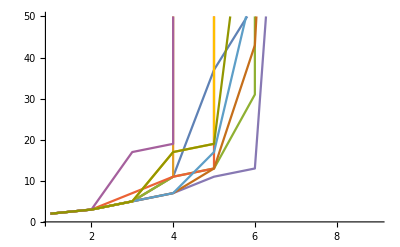

```mathematica
ListPlot[{{2,3,5,11,37,53,2389,5113},{2,3,5,11,131773807453},{2,3,5,11,13,31,359574015457},{2,3,7,11,13,615883,1279253},{2,3,5,7,11,13,149,163,2655313},{2,3,5,7,13,43,227,2369709631},{2,3,5,7,17,59,401,99608657},{2,3,5,17,19,72577,371362711},{2,3,17,19,277198069520951},{2,3,5,17,19,97,5906622912763}},Joined->True,PlotRange->{All,{0,50}}]
```

```mathematica
FactorInteger[1171866665945217354372]
```

{{2,2},{3,3},{13,1},{41,1},{24623,1},{826772973001,1}}

```mathematica
FactorInteger[3788033204198323080]
```

{{2,3},{3,2},{5,1},{7,1},{11,1},{13,1},{149,1},{163,2},{2655313,1}}

```mathematica
PowerCoeff[ChromaticPolynomial[allGraphs5[39366,"graph"],x],5]/5
```

{125,100,30,4,1/5}

```mathematica
162+81
```

243

```mathematica
PowerCoeff[(-3+x)^3]
```

First::normal: Nonatomic expression expected at position 1 in First[a].

General::stop: Further output of First::normal will be suppressed during this calculation.

{(-3+x)^3-(7+(-5+x) x) First[a],First[a],First[a],First[a]}

```mathematica
Transpose[{{6},{23},{40},{57},{74},{91},{108},{125},{142},{159},{176},{193},{210},{227},{244},{261},{278},{295}}]//First//Differences
```

{17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17}

## More play

```mathematica
ChromaticPolynomial[MinimalGraph[3],3]
```

0

```mathematica
TableForm[Table[With[
{chrom=ChromaticPolynomial[MinimalGraph[k],x]},
(chrom/.x->4)->MatrixForm[Table[PowerCoeff[chrom,n]->Total[PowerCoeff[chrom,n]],{n,0,5}]]
],{k,8}]//Sort,TableDepth->2]
```

24→({0,2,-3,1}→0
{0,-1,0,1}→0
{0,2,3,1}→6
{6,11,6,1}→24
{24,26,9,1}→60
{60,47,12,1}→120)
24→({0,2,-3,1}→0
{0,-1,0,1}→0
{0,2,3,1}→6
{6,11,6,1}→24
{24,26,9,1}→60
{60,47,12,1}→120)
24→({0,-6,11,-6,1}→0
{0,2,-1,-2,1}→0
{0,-2,-1,2,1}→0
{0,6,11,6,1}→24
{24,50,35,10,1}→120
{120,154,71,14,1}→360)
24→({0,18,-39,29,-9,1}→0
{0,-4,4,3,-4,1}→0
{0,2,-1,-3,1,1}→0
{0,0,6,11,6,1}→24
{24,74,85,45,11,1}→240
{240,428,296,99,16,1}→1080)
24→({0,-54,135,-126,56,-12,1}→0
{0,8,-12,-2,11,-6,1}→0
{0,-2,3,2,-4,0,1}→0
{0,0,0,6,11,6,1}→24
{24,98,159,130,56,12,1}→480
{480,1096,1020,494,131,18,1}→3240)
24→({0,162,-459,513,-294,92,-15,1}→0
{0,-16,32,-8,-24,23,-8,1}→0
{0,2,-5,1,6,-4,-1,1}→0
{0,0,0,0,6,11,6,1}→24
{24,122,257,289,186,68,13,1}→960
{960,2672,3136,2008,756,167,20,1}→9720)
24→({0,-486,1539,-1998,1395,-570,137,-18,1}→0
{0,32,-80,48,40,-70,39,-10,1}→0
{0,-2,7,-6,-5,10,-3,-2,1}→0
{0,0,0,0,0,6,11,6,1}→24
{24,146,379,546,475,254,81,14,1}→1920
{1920,6304,8944,7152,3520,1090,207,22,1}→29160)
24→({0,1458,-5103,7533,-6183,3105,-981,191,-21,1}→0
{0,-64,192,-176,-32,180,-148,59,-12,1}→0
{0,2,-9,13,-1,-15,13,-1,-3,1}→0
{0,0,0,0,0,0,6,11,6,1}→24
{24,170,525,925,1021,729,335,95,15,1}→3840
{3840,14528,24192,23248,14192,5700,1504,251,24,1}→87480)

```mathematica
TableForm[Table[With[
{chrom=ChromaticPolynomial[JacobsThalGraph[k],x]},
(chrom/.x->4)->MatrixForm[Table[PowerCoeff[chrom,n]->Total[PowerCoeff[chrom,n]],{n,0,5}]]
],{k,8}]//Tally//Sort,TableDepth->2]
```

24→({0,18,-39,29,-9,1}→0
{0,-4,4,3,-4,1}→0
{0,2,-1,-3,1,1}→0
{0,0,6,11,6,1}→24
{24,74,85,45,11,1}→240
{240,428,296,99,16,1}→1080) | 1
96→({0,-64,154,-137,58,-12,1}→0
{0,11,-14,-5,13,-6,1}→0
{0,-4,4,7,-2,0,1}→6
{6,23,28,19,13,6,1}→96
{96,224,238,151,58,12,1}→780
{780,1451,1174,523,133,18,1}→4080) | 1
120→({0,210,-565,594,-320,95,-15,1}→0
{0,-26,43,-1,-35,26,-8,1}→0
{0,6,-9,-6,10,-1,-1,1}→0
{0,6,29,39,25,14,6,1}→120
{120,394,547,434,220,71,13,1}→1800
{1800,4110,4095,2319,805,170,20,1}→13320) | 1
288→({0,-664,1992,-2432,1595,-615,141,-18,1}→0
{0,57,-119,44,75,-91,43,-10,1}→0
{0,-8,16,0,-15,13,1,-2,1}→6
{6,29,57,76,65,33,15,6,1}→288
{288,936,1384,1232,735,305,85,14,1}→4980
{4980,12481,14137,9468,4095,1165,211,22,1}→46560) | 1
504→({0,2058,-6839,9533,-7378,3500,-1050,196,-21,1}→0
{0,-120,306,-211,-112,266,-182,64,-12,1}→0
{0,10,-25,13,14,-28,14,4,-3,1}→0
{0,12,64,125,140,98,42,16,6,1}→504
{504,1986,3429,3485,2366,1148,406,100,15,1}→13440
{13440,37768,48206,36973,18872,6650,1610,256,24,1}→163800) | 1
1056→({0,-6304,23030,-36115,32228,-18158,6734,-1652,260,-24,1}→0
{0,247,-748,741,14,-658,644,-316,89,-14,1}→0
{0,-12,36,-35,0,42,-42,12,8,-4,1}→6
{6,35,98,197,266,238,140,52,17,6,1}→1056
{1056,4480,8594,9837,7532,4130,1694,524,116,16,1}→37980
{37980,116871,164880,141445,82278,34062,10164,2148,305,26,1}→590160) | 1
2040→({0,19170,-76425,133172,-134592,87822,-38808,11802,-2448,333,-27,1}→0
{0,-502,1765,-2257,726,1344,-1974,1296,-501,118,-16,1}→0
{0,14,-49,68,-36,-42,84,-54,6,13,-5,1}→0
{0,18,111,287,462,504,378,192,63,18,6,1}→2040
{2040,9818,21223,27380,23640,14574,6720,2394,660,133,17,1}→108600
{108600,365570,566105,536207,347958,163632,57162,14832,2787,358,28,1}→2163240) | 1
4128→({0,-58024,250756,-480554,542325,-402090,206262,-74886,19290,-3465,415,-30,1}→0
{0,1013,-4061,6326,-3750,-1962,5334,-4614,2325,-745,151,-18,1}→0
{0,-16,64,-114,105,6,-126,138,-60,-5,19,-6,1}→6
{6,41,151,406,750,966,882,570,255,75,19,6,1}→4128
{4128,21656,51820,74726,72525,50310,25998,10362,3270,815,151,18,1}→315780
{315780,1154861,1950571,2023446,1446450,756870,299502,90714,20865,3535,415,30,1}→8063040) | 1